# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

LARIN METHOD mass leptons MM=0, box diagrams with GAUGE=1

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

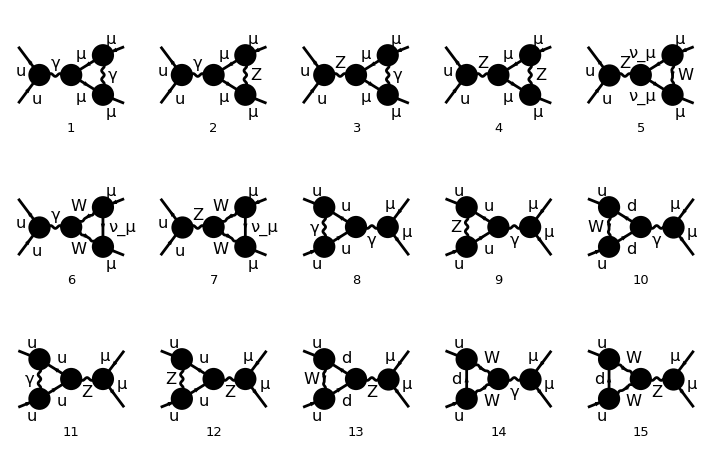

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

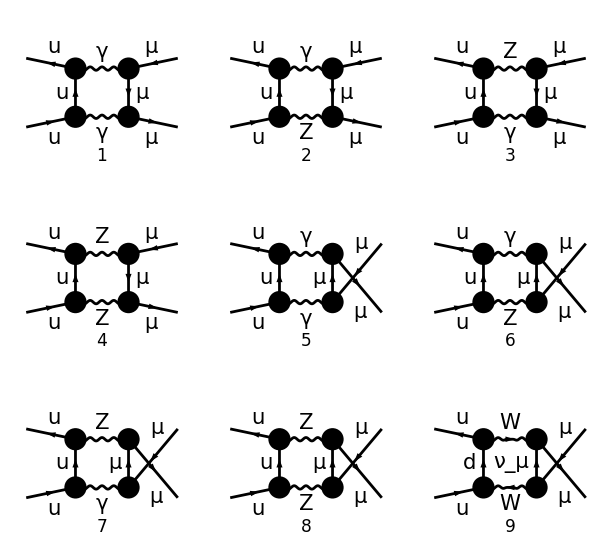

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

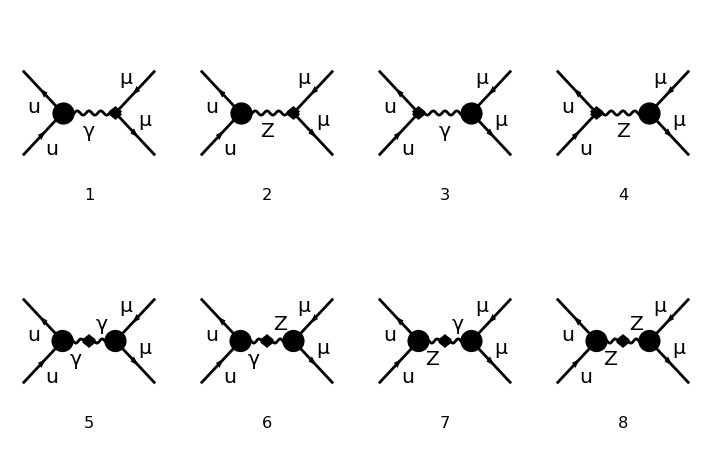

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[4][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[4][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];
```

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).gs[-(p2)+q1+k2].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k1,0] FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k2)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).gs[p2-q1-k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).v[k1,0] FeynAmpDenominator[1/(-MZ2+(p2-q1)^2),1/(q1)^2,1/(p2-q1-k1)^2,1/(-MZ2+(p2-q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*confronto Nar.*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[-(p1)+q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).v[k1,MM] FeynAmpDenominator[1/(p1-q1)^2,1/(p1+p2-q1)^2,1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[p2-q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,MM].(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).(MM+gs[q1-k1]).(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).v[k1,MM] FeynAmpDenominator[1/(p2-q1)^2,1/(p1+p2-q1)^2,1/(q1)^2,1/(-MM2+(-(q1)+k1)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{2}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.NonCommutative[DiracMatrix[Index[Lorentz,bn1_]],ChiralityProjector[n_]]->NonCommutative[ChiralityProjector[n],DiracMatrix[Index[Lorentz,bn1]]]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(-(ⅈ EL (I3U-QZUl SW2) om_-.ga[Lorbn1])/(CW SW)+(ⅈ EL QZUr SW om_+.ga[Lorbn1])/CW).u[p1,0]],CONJ[ū[k1,0].(-(ⅈ EL (I3L-QZLl SW2) om_-.ga[Lorbn2])/(CW SW)+(ⅈ EL QZLr SW om_+.ga[Lorbn2])/CW).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Semplificazione propagatori

Divisione in termini dipendenti da gauge e indipendenti

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
(*box w*)
wnumerat=DeleteCases[wwbox, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify
```

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k2)^2 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MW2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MW2+(p2-q1-k1-k2)^2))/(16 π^4)

```mathematica
(*prove semplificaz propagatore generico*)
sempp[propag_]:=Module[{t1,t11,t111,t1111,t2,t22,t222,t2222,tnumerat1,tnumerat2,t1w,t11w,t111w,t1111w,t2w,t22w,t222w,t2222w,tnumerat1w,tnumerat2w},
propagatore=propag;
tnn=Select[propagatore,MemberQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini contenenti ZGAUGE oppure massa MZ*)
tnn2=Select[propagatore,FreeQ[#,ZGAUGE|MZ,Infinity]&];(*seleziona i termini restanti, passaggio intermedio*)
	tnnw=Select[tnn2,MemberQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini contenenti WGAUGE oppure massa MW in tnn2*)
	tnnrest=Select[tnn2,FreeQ[#,WGAUGE|MW,Infinity]&];(*seleziona i termini restanti*)
(*propagatore=tnn*tnnw*tnnrest*)

(*ZGAUGE*)
Which[Length[tnn]===2,(*caso di diagrammi con γ e Z*)
	t1=tnn//Expand;
	t11=numer/@t1/.numer->Sequence//Simplify;
	t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
	tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum=tnumerat1,

	Length[tnn]>2,(*caso con 2 Z*)
		t1=tnn[[1;;Length[tnn]/2]]//Expand;
		t11=numer/@t1/.numer->Sequence//Simplify;
		t111=Collect[t11,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111=Collect[t111,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1=t1111//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];

		t2=tnn[[Length[tnn]/2+1;;Length[tnn]]]//Expand;
		t22=numer/@t2/.numer->Sequence//Simplify;
		t222=Collect[t22,PropagatorDenominator[x_,mzg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t2222=Collect[t222,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat2=t2222//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]]->FourVector[a + b, Index[w]];
		totnum=tnumerat1*tnumerat2,

	True,
		totnum=1];

(*WGAUGE*)
Which[Length[tnnw]===2,(*caso di diagrammi con un solo W*)
		t1w=tnnw//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.ZGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->ZGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
		totnum1=tnumerat1w,

	Length[tnnw]>2,(*caso con 2 W*)
		t1w=tnnw[[1;;Length[tnnw]/2]]//Expand;
		t11w=numerw/@t1w/.numerw->Sequence//Simplify;
		t111w=Collect[t11w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
		t1111w=Collect[t111w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
		tnumerat1w=t1111w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];

	t2w=tnnw[[Length[tnnw]/2+1;;Length[tnnw]]]//Expand;
	t22w=numerw/@t2w/.numerw->Sequence//Simplify;
	t222w=Collect[t22w,PropagatorDenominator[x_,mwg],FullSimplify]//.WGAUGE->Zm1+1//.FourVector[a__]:>Distribute[FourVector[a]];
	t2222w=Collect[t222w,Zm1,Simplify]//.FourVector[a__,b_]-FourVector[a__,b_]->0//.Zm1->WGAUGE-1;
	tnumerat2w=t2222w//.FourVector[a_, Index[w__]]+FourVector[b_, Index[w__]] ->FourVector[a + b, Index[w]];
	totnum1=tnumerat1w*tnumerat2w,

	True,
		totnum1=1];


propagtot=totnum*totnum1*tnnrest];
```

```mathematica
tpropag=sempp[tnumerat]
upropag=sempp[unumerat]
wpropag=sempp[wnumerat]
```

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k2)^2 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MZ2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MZ2+(p2-q1-k1-k2)^2))/(16 π^4)

(ⅈ g[Lor1,Lor2] g[Lor3,Lor4] 1/(-MW2+(p2-q1)^2) 1/(q1)^2 1/(p2-q1-k1)^2 1/(-MW2+(p2-q1-k1-k2)^2))/(16 π^4)

```mathematica
nn=7;
denomt=tnumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
denomu=unumerat[[nn]]/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

1/(p2-q1-k2)^2

1/(p2-q1-k1)^2

```mathematica
(*propagatore born*)
bornpropag2
(*propagatore box, parte in comune fra t e u. propagatore box W*)
propagatT=tnumerat[[nn]];
propagatU=unumerat[[nn]];

ptot=DeleteCases[tpropag,propagatT,Infinity]+DeleteCases[upropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
ptotw=DeleteCases[wpropag,propagatU,Infinity]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(8 π^4 (-MZ2+(p2-q1)^2) (q1)^2 (-MZ2+(p2-q1-k1-k2)^2))

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (-MW2+(p2-q1)^2) (q1)^2 (-MW2+(p2-q1-k1-k2)^2))

#### Trace

```mathematica
trg2[s___,MM,u___]:=MM trg2[s,u];
trg2[s___,-MM,u___]:=-MM trg2[s,u];
trg[s___,MM,u___]:=MM trg[s,u];
trg[z___,-G5]:=-trg[z,G5];
trg[a_,b_,G5]:=0;
trg[a_,b_,c_,d_,G5]:=-4 I LC myEps[a,b,c,d];
trg[x___,G5,G5,y___]:=trg[x,y];
trg[x__,G5]:=0/;OddQ[Length[{x}]];
trg[q___,G5,y__]:=trg[q,y,G5](-1)^(Length[{y}]);
trg[a_,b_]:=4 SP[a,b];
trg[w__]:=0/;OddQ[Length[{w}]] && FreeQ[{w},G5];

(*TRACE*)
trg[x__]:=Module[{temp,temp1,temp2,i,temp3},

temp={x};
temp1=Delete[temp,1];
temp2=Table[Delete[temp1,i],{i,1,Length[temp1]}];
temp3=Sum[SP[temp[[1]],temp1[[i]]](-1)^(i+1)*Apply[trg,temp2[[i]]],{i,1,Length[temp2]}];
temp3=Expand[temp3];

temp3
];
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
```

```mathematica
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracMatrix[b],y]/;Head[b]=!=FourMomentum;
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracSlash[b],y]/;Head[b]===FourMomentum;
```

```mathematica
SP/:SP[Q1,Q1]:=Q1^2;
SP/: SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
 SP/:SP[P1,K1]:=(-T)/2; 
SP/:SP[P2,K2]:=(-T)/2;
SP/: SP[P1,K2]:=(-U)/2; SP/:SP[P2,K1]:=(-U)/2
```

```mathematica
(*CASO MASSLESS*)
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
(*trd2[x___,DiracSlash[s_],DiracMatrix[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracMatrix[t],y];
trd2[x___,DiracSlash[s_],DiracSlash[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracSlash[t],y];*)

TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=0;
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=0;
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
       
TR[a_,b_]= 4 SP[a,b];
```

```mathematica
gggg=traceff4[DiracSlash[Times[-1,FourMomentum[Incoming,1]]],DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g15]],DiracMatrix[Index[Lorentz,g7]],DiracMatrix[Index[Lorentz,g3]],DiracMatrix[Index[Lorentz,g6]],DiracSlash[Times[-1,FourMomentum[Incoming,1]]],DiracMatrix[Index[Lorentz,g1]](*,DiracMatrix[Index[Lorentz,g1]]*)]
R1=%//.traceff4->trd//.simptrd//.trd->trg//.SP[P1,P1]->0//Simplify
gggg//.traceff4->TR//.{SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]/;Head[b]=!=FourMomentum->sp*TR[x,DiracMatrix[b],y],SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]/;Head[b]===FourMomentum->sp*TR[x,DiracSlash[b],y],TR[x__]/;Length[{x}]===1->0}
R2=%//.TR->trg//Simplify
R1-R2//Simplify
```

traceff4[gs[-(p1)],ga[Lorg2],ga[Lorg15],ga[Lorg7],ga[Lorg3],ga[Lorg6],gs[-(p1)],ga[Lorg1]]

-8 SP[p1,Lorg1] (SP[p1,Lorg3] SP[Lorg15,Lorg7] SP[Lorg2,Lorg6]-SP[p1,Lorg3] SP[Lorg15,Lorg6] SP[Lorg2,Lorg7]-SP[p1,Lorg2] SP[Lorg15,Lorg7] SP[Lorg3,Lorg6]+SP[p1,Lorg15] SP[Lorg2,Lorg7] SP[Lorg3,Lorg6]+SP[p1,Lorg7] (SP[Lorg15,Lorg6] SP[Lorg2,Lorg3]-SP[Lorg15,Lorg3] SP[Lorg2,Lorg6]-SP[Lorg15,Lorg2] SP[Lorg3,Lorg6])-SP[p1,Lorg2] SP[Lorg15,Lorg6] SP[Lorg3,Lorg7]+SP[p1,Lorg15] SP[Lorg2,Lorg6] SP[Lorg3,Lorg7]-SP[p1,Lorg6] (SP[Lorg15,Lorg7] SP[Lorg2,Lorg3]-SP[Lorg15,Lorg3] SP[Lorg2,Lorg7]+SP[Lorg15,Lorg2] SP[Lorg3,Lorg7])+SP[p1,Lorg3] SP[Lorg15,Lorg2] SP[Lorg6,Lorg7]+SP[p1,Lorg2] SP[Lorg15,Lorg3] SP[Lorg6,Lorg7]-SP[p1,Lorg15] SP[Lorg2,Lorg3] SP[Lorg6,Lorg7])

2 SP[p1,Lorg2] TR[ga[Lorg15],ga[Lorg7],ga[Lorg3],ga[Lorg6],gs[p1],ga[Lorg1]]+2 SP[p1,Lorg7] TR[ga[Lorg2],ga[Lorg15],ga[Lorg3],ga[Lorg6],gs[p1],ga[Lorg1]]+2 SP[p1,Lorg6] TR[ga[Lorg2],ga[Lorg15],ga[Lorg7],ga[Lorg3],gs[p1],ga[Lorg1]]-2 SP[p1,Lorg3] TR[ga[Lorg2],ga[Lorg15],ga[Lorg7],ga[Lorg6],gs[p1],ga[Lorg1]]-2 SP[p1,Lorg15] TR[ga[Lorg2],ga[Lorg7],ga[Lorg3],ga[Lorg6],gs[p1],ga[Lorg1]]

8 SP[p1,Lorg1] (-SP[p1,Lorg3] SP[Lorg15,Lorg7] SP[Lorg2,Lorg6]+SP[p1,Lorg3] SP[Lorg15,Lorg6] SP[Lorg2,Lorg7]+SP[p1,Lorg2] SP[Lorg15,Lorg7] SP[Lorg3,Lorg6]-SP[p1,Lorg15] SP[Lorg2,Lorg7] SP[Lorg3,Lorg6]+SP[p1,Lorg7] (-SP[Lorg15,Lorg6] SP[Lorg2,Lorg3]+SP[Lorg15,Lorg3] SP[Lorg2,Lorg6]+SP[Lorg15,Lorg2] SP[Lorg3,Lorg6])+SP[p1,Lorg2] SP[Lorg15,Lorg6] SP[Lorg3,Lorg7]-SP[p1,Lorg15] SP[Lorg2,Lorg6] SP[Lorg3,Lorg7]+SP[p1,Lorg6] (SP[Lorg15,Lorg7] SP[Lorg2,Lorg3]-SP[Lorg15,Lorg3] SP[Lorg2,Lorg7]+SP[Lorg15,Lorg2] SP[Lorg3,Lorg7])-SP[p1,Lorg3] SP[Lorg15,Lorg2] SP[Lorg6,Lorg7]-SP[p1,Lorg2] SP[Lorg15,Lorg3] SP[Lorg6,Lorg7]+SP[p1,Lorg15] SP[Lorg2,Lorg3] SP[Lorg6,Lorg7])

0

```mathematica
(*index of initial state:*)
(*sost*)
larin2i=myEps[Index[Lorentz,g1],Index[Lorentz,g2],Index[Lorentz,g3],Index[Lorentz,g4]]myEps[Index[Lorentz,g5],Index[Lorentz,g6],
Index[Lorentz,g7],Index[Lorentz,g8]]myEps[Index[Lorentz,gc1],Index[Lorentz,gc2],Index[Lorentz,gc3],Index[Lorentz,gc4]]traceff4[x,DiracMatrix[Index[Lorentz,g1]],
DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g3]],DiracMatrix[Index[Lorentz,g4]],y,
DiracMatrix[Index[Lorentz,g5]],DiracMatrix[Index[Lorentz,g6]],DiracMatrix[Index[Lorentz,g7]],DiracMatrix[Index[Lorentz,g8]],o,
DiracMatrix[Index[Lorentz,gc4]],DiracMatrix[Index[Lorentz,gc3]],DiracMatrix[Index[Lorentz,gc2]],DiracMatrix[Index[Lorentz,gc1]],w];

larin22i=myEps[Index[Lorentz,g1],Index[Lorentz,g2],Index[Lorentz,g3],Index[Lorentz,g4]]myEps[Index[Lorentz,gc1],
Index[Lorentz,gc2],Index[Lorentz,gc3],Index[Lorentz,gc4]]traceff4[x,DiracMatrix[Index[Lorentz,g1]],DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g3]],
DiracMatrix[Index[Lorentz,g4]],y,DiracMatrix[Index[Lorentz,gc4]],DiracMatrix[Index[Lorentz,gc3]],DiracMatrix[Index[Lorentz,gc2]],DiracMatrix[Index[Lorentz,gc1]],w];

larin222i=myEps[Index[Lorentz,g1],Index[Lorentz,g2],Index[Lorentz,g3],Index[Lorentz,g4]]myEps[Index[Lorentz,g5],
Index[Lorentz,g6],Index[Lorentz,g7],Index[Lorentz,g8]]traceff4[x,DiracMatrix[Index[Lorentz,g1]],DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g3]],
DiracMatrix[Index[Lorentz,g4]],y,DiracMatrix[Index[Lorentz,g5]],DiracMatrix[Index[Lorentz,g6]],DiracMatrix[Index[Lorentz,g7]],DiracMatrix[Index[Lorentz,g8]],w];

(*considerando complex conjugate, ordine inverso delle matrici abcd->dcba*)

LARIN2={
(*3 g5*)
traceff4[x___,G5,y___,G5,o___,con G5,w___]->fg53*I/24*I/24*-I/24*larin2i,
traceff4[x___,-G5,y___,G5,o___,con G5,w___]->fg53*-I/24*I/24*-I/24*larin2i,
traceff4[x___,G5,y___,-G5,o___,con G5,w___]->fg53*I/24*-I/24*-I/24*larin2i,
traceff4[x___,G5,y___,G5,o___,-con G5,w___]->fg53*I/24*I/24*I/24*larin2i,
traceff4[x___,-G5,y___,-G5,o___,con G5,w___]->fg53*-I/24*-I/24*-I/24*larin2i,
traceff4[x___,G5,y___,-G5,o___,-con G5,w___]->fg53*I/24*-I/24*I/24*larin2i,
traceff4[x___,-G5,y___,G5,o___,-con G5,w___]->fg53*-I/24*I/24*I/24*larin2i,
traceff4[x___,-G5,y___,-G5,o___,-con G5,w___]->fg53*-I/24*-I/24*I/24*larin2i,

(*2 g5 in2 *)
traceff4[x___,G5,y___,con G5,w___]->fg52*I/24*-I/24*larin22i,
traceff4[x___,-G5,y___,con G5,w___]->fg52*-I/24*-I/24*larin22i,
traceff4[x___,G5,y___,-con G5,w___]->fg52*I/24*I/24*larin22i,
traceff4[x___,-G5,y___,-con G5,w___]->fg52*-I/24*I/24*larin22i,

traceff4[x___,G5,y___, G5,w___]->fg52*I/24*I/24*larin222i,
traceff4[x___,-G5,y___,G5,w___]->fg52*-I/24*I/24*larin222i,
traceff4[x___,G5,y___,- G5,w___]->fg52*I/24*-I/24*larin222i,
traceff4[x___,-G5,y___,-G5,w___]->fg52*-I/24*-I/24*larin222i,

(*conj 1 g5*)
traceff4[x___,con G5,w___]->fg51*-I/24 myEps[Index[Lorentz,gc1],Index[Lorentz,gc2],Index[Lorentz,gc3],Index[Lorentz,gc4]]
traceff4[x,DiracMatrix[Index[Lorentz,gc4]],DiracMatrix[Index[Lorentz,gc3]],DiracMatrix[Index[Lorentz,gc2]],DiracMatrix[Index[Lorentz,gc1]],w],
traceff4[x___,-con G5,w___]->fg51*I/24 myEps[Index[Lorentz,gc1],Index[Lorentz,gc2],Index[Lorentz,gc3],Index[Lorentz,gc4]]
traceff4[x,DiracMatrix[Index[Lorentz,gc4]],DiracMatrix[Index[Lorentz,gc3]],DiracMatrix[Index[Lorentz,gc2]],DiracMatrix[Index[Lorentz,gc1]],w],
(*born 1 g5*)
traceff4[x___, G5,w___]->fg51*I/24 myEps[Index[Lorentz,g1],Index[Lorentz,g2],Index[Lorentz,g3],Index[Lorentz,g4]]
traceff4[x,DiracMatrix[Index[Lorentz,g1]],DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g3]],DiracMatrix[Index[Lorentz,g4]],w],
traceff4[x___, -G5,w___]->fg51*-I/24 myEps[Index[Lorentz,g1],Index[Lorentz,g2],Index[Lorentz,g3],Index[Lorentz,g4]]
traceff4[x,DiracMatrix[Index[Lorentz,g1]],DiracMatrix[Index[Lorentz,g2]],DiracMatrix[Index[Lorentz,g3]],DiracMatrix[Index[Lorentz,g4]],w]
};
```

```mathematica
(*sost*)
larin2f=myEps[Index[Lorentz,f1],Index[Lorentz,f2],Index[Lorentz,f3],Index[Lorentz,f4]]*myEps[Index[Lorentz,f5],
Index[Lorentz,f6],Index[Lorentz,f7],Index[Lorentz,f8]]*myEps[Index[Lorentz,fc1],Index[Lorentz,fc2],Index[Lorentz,fc3],Index[Lorentz,fc4]]traceff4[x,
DiracMatrix[Index[Lorentz,f1]],DiracMatrix[Index[Lorentz,f2]],DiracMatrix[Index[Lorentz,f3]],DiracMatrix[Index[Lorentz,f4]],y,
DiracMatrix[Index[Lorentz,f5]],DiracMatrix[Index[Lorentz,f6]],DiracMatrix[Index[Lorentz,f7]],DiracMatrix[Index[Lorentz,f8]],o,
DiracMatrix[Index[Lorentz,fc4]],DiracMatrix[Index[Lorentz,fc3]],DiracMatrix[Index[Lorentz,fc2]],DiracMatrix[Index[Lorentz,fc1]],w];
larin22f=
myEps[Index[Lorentz,f1],Index[Lorentz,f2],Index[Lorentz,f3],Index[Lorentz,f4]]myEps[Index[Lorentz,fc1],Index[Lorentz,fc2],Index[Lorentz,fc3],
Index[Lorentz,fc4]]traceff4[x,DiracMatrix[Index[Lorentz,f1]],DiracMatrix[Index[Lorentz,f2]],DiracMatrix[Index[Lorentz,f3]],DiracMatrix[Index[Lorentz,f4]],y,
DiracMatrix[Index[Lorentz,fc4]],DiracMatrix[Index[Lorentz,fc3]],DiracMatrix[Index[Lorentz,fc2]],DiracMatrix[Index[Lorentz,fc1]],w];
larin222f=
myEps[Index[Lorentz,f1],Index[Lorentz,f2],Index[Lorentz,f3],Index[Lorentz,f4]]myEps[Index[Lorentz,f5],Index[Lorentz,f6],Index[Lorentz,f7],
Index[Lorentz,f8]]traceff4[x,DiracMatrix[Index[Lorentz,f1]],DiracMatrix[Index[Lorentz,f2]],DiracMatrix[Index[Lorentz,f3]],DiracMatrix[Index[Lorentz,f4]],y,
DiracMatrix[Index[Lorentz,f5]],DiracMatrix[Index[Lorentz,f6]],DiracMatrix[Index[Lorentz,f7]],DiracMatrix[Index[Lorentz,f8]],w];


LARIN2F={
(*3 g5*)
traceff4[x___,G5,y___,G5,o___,con G5,w___]->fg53*I/24*I/24*-I/24*larin2f,
traceff4[x___,-G5,y___,G5,o___,con G5,w___]->fg53*-I/24*I/24*-I/24*larin2f,
traceff4[x___,G5,y___,-G5,o___,con G5,w___]->fg53*I/24*-I/24*-I/24*larin2f,
traceff4[x___,G5,y___,G5,o___,-con G5,w___]->fg53*I/24*I/24*I/24*larin2f,
traceff4[x___,-G5,y___,-G5,o___,con G5,w___]->fg53*-I/24*-I/24*-I/24*larin2f,
traceff4[x___,G5,y___,-G5,o___,-con G5,w___]->fg53*I/24*-I/24*I/24*larin2f,
traceff4[x___,-G5,y___,G5,o___,-con G5,w___]->fg53*-I/24*I/24*I/24*larin2f,
traceff4[x___,-G5,y___,-G5,o___,-con G5,w___]->fg53*-I/24*-I/24*I/24*larin2f,

(*2 g5 fi *)
traceff4[x___,G5,y___,con G5,w___]->fg52*I/24*-I/24*larin22f,
traceff4[x___,-G5,y___,con G5,w___]->fg52*-I/24*-I/24*larin22f,
traceff4[x___,G5,y___,-con G5,w___]->fg52*-I/24*I/24*larin22f,
traceff4[x___,-G5,y___,-con G5,w___]->fg52*-I/24*I/24*larin22f,

traceff4[x___,G5,y___, G5,w___]->fg52*I/24*I/24*larin222f,
traceff4[x___,-G5,y___, G5,w___]->fg52*-I/24*I/24*larin222f,
traceff4[x___,G5,y___,-G5,w___]->fg52*-I/24*-I/24*larin222f,
traceff4[x___,-G5,y___,-G5,w___]->fg52*-I/24*-I/24*larin222f,

(*conj*)
traceff4[x___,con G5,w___]->fg51*-I/24 myEps[Index[Lorentz,fc1],Index[Lorentz,fc2],Index[Lorentz,fc3],Index[Lorentz,fc4]]
traceff4[x,DiracMatrix[Index[Lorentz,fc4]],DiracMatrix[Index[Lorentz,fc3]],DiracMatrix[Index[Lorentz,fc2]],DiracMatrix[Index[Lorentz,fc1]],w],
traceff4[x___,-con G5,w___]->fg51*I/24 myEps[Index[Lorentz,fc1],Index[Lorentz,fc2],Index[Lorentz,fc3],Index[Lorentz,fc4]]
traceff4[x,DiracMatrix[Index[Lorentz,fc4]],DiracMatrix[Index[Lorentz,fc3]],DiracMatrix[Index[Lorentz,fc2]],DiracMatrix[Index[Lorentz,fc1]],w],
(*born*)
traceff4[x___,G5,w___]->fg51*I/24 myEps[Index[Lorentz,f1],Index[Lorentz,f2],Index[Lorentz,f3],Index[Lorentz,f4]]
traceff4[x,DiracMatrix[Index[Lorentz,f1]],DiracMatrix[Index[Lorentz,f2]],DiracMatrix[Index[Lorentz,f3]],DiracMatrix[Index[Lorentz,f4]],w],
traceff4[x___,-G5,w___]->fg51*-I/24 myEps[Index[Lorentz,f1],Index[Lorentz,f2],Index[Lorentz,f3],Index[Lorentz,f4]]
traceff4[x,DiracMatrix[Index[Lorentz,f1]],DiracMatrix[Index[Lorentz,f2]],DiracMatrix[Index[Lorentz,f3]],DiracMatrix[Index[Lorentz,f4]],w]

};
```

```mathematica
tr1i=Table[traceff4[stati[[i]]/.List->Sequence],{i,1,Length[stati]}](*//.traceff4->move2*);(*sposto proiettori in fondo*)
chii=Delete[chi,Position[tr1i,0,{1}]];(*cariche*)
tr2i=Map[Distribute,1/4 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
iiiii=DeleteCases[DeleteCases[tr2i,1,{4}]//.LARIN2,con,Infinity];
```

```mathematica
fffff[[1,89]]//Expand;
%//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->trd//Expand;
R1=Timing[%//.trd->trg//.SP[P1,P1]->0];
```

```mathematica
fffff[[1,89]]//Expand;
%//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->TR//ExpandAll//Simplify
```

-1/2304 ⅈ (48-94 d+59 d^2-14 d^3+d^4) fg53 MM2 myEps[Lorfc1,Lorfc2,Lorfc3,Lorfc4] TR[gs[k2],ga[Lor4],ga[Lor2],ga[Lorfc4],ga[Lorfc3],ga[Lorfc2],ga[Lorfc1],ga[Lorbn2]]

```mathematica
R2=Timing[%//.TR->trg];
(*%//.{SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]/;Head[b]=!=FourMomentum->sp*TR[x,DiracMatrix[b],y],SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]/;Head[b]===FourMomentum->sp*TR[x,DiracSlash[b],y],TR[x__]/;Length[{x}]===1->0}*)
```

```mathematica
R1[[2]]-R2[[2]]//Simplify
```

0

```mathematica
R1[[1]]
R2[[1]]
```

737.617

0.032917

```mathematica
tr3i=Apply[Plus,Table[Table[iip0=iiiii[[m,l]]//Expand;
iip=iip0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->trd//Expand(*simplify with SP*);
iip=iip//.simptrd;
If[Head[iip]===Plus,
iip2=Table[For[i=1;t=iip[[j]],i<=Length[Select[iip[[j]],Head[#]===trd&,Infinity]],i++,
t=Map[If[Head[#]===trd,Append[Drop[#,1],First[#]],#]&,t,Infinity]//.simptrd];t,{j,1,Length[iip]}]/.List->Plus//Simplify,
iip2=iip];
iip2,{l,1,Length[iiiii[[m]]]}],{m,1,Length[iiiii]}],{1}];
```

```mathematica
tr4i=tr3i//.trd->trg//.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
```

$Aborted

```mathematica
tr4i=tr3i//.trd->trg//.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
tracciai=tr4i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//Expand;
```

```mathematica
(*stato f*)
tr1f=Table[traceff4[statf[[i]]/.List->Sequence],{i,1,Length[statf]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True];
If[FreeQ[statf,MM,Infinity],
chff=Delete[chf,Position[tr1f,0,{1}]],
chff=chf];(*cariche*)
tr2f=Flatten[Map[Distribute,1/4 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity(*{4}*)]];
(*gamma5gamma5=1*)
fffff=DeleteCases[DeleteCases[tr2f,1,{4}]//.LARIN2F,con,Infinity];
```

```mathematica
tr3f=Apply[Plus,Table[Table[ffp0=fffff[[m,l]]//Expand;
ffp=ffp0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->trd//Expand(*simplify with SP*);
ffp=ffp//.simptrd;
If[Head[ffp]===Plus,
ffp2=Table[For[i=1;t=ffp[[j]],i<=Length[Select[ffp[[j]],Head[#]===trd&,Infinity]],i++,
t=Map[If[Head[#]===trd,Append[Drop[#,1],First[#]],#]&,t,Infinity]//.simptrd];t,{j,1,Length[ffp]}]/.List->Plus//Simplify,
ffp2=ffp];
ffp2,{l,1,Length[fffff[[m]]]}],{m,1,Length[fffff]}],{1}];
```

```mathematica
(*Prova traceff con mom k1 e p1 >0 v vbar->p-m uubar->p+m*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];

(*SIMPLIFY trd*)
simptrd={SP[a_,b_]*sp___*trd[x___,DiracMatrix[a_],y___]->sp*trd[x,DiracMatrix[b],y],trd[x__]/;Length[{x}]===1->0};
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{i,tr1i,tr2i,tr3i,tr4i,tr1f,tr2f,tr3f,tr4f,tracciai,tracciaf,chii,chff},

(*Prova traceff con mom k1 e p1 >0 v vbar->p-m uubar->p+m*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,MM,b___]:=MM traceff4[a,b];
traceff4[a___,-MM,b___]:=-MM traceff4[a,b];

(*SIMPLIFY trd*)
simptrd={SP[a_,b_]*sp___*trd[x___,DiracMatrix[a_],y___]->sp*trd[x,DiracMatrix[b],y],trd[x__]/;Length[{x}]===1->0};

(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}];
tr2i=Map[Distribute,1/6 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
iiiii=DeleteCases[DeleteCases[tr2i,1,{4}]//.LARIN2,con,Infinity];

tr3i=Apply[Plus,Table[Table[iip0=iiiii[[m,l]]//Expand;
iip=iip0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->TR//ExpandAll;
iip,{l,1,Length[iiiii[[m]]]}],{m,1,Length[iiiii]}],{1}];
tr4i=tr3i//.TR->trg;
(*tr4i=tr3i//.trd->trg//.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;*)
tracciai=tr4i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}(*//Expand*);

Print["stato i ",1/6 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr1f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True];
tr2f=Flatten[Map[Distribute,1/6 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity(*{4}*)]];
(*gamma5gamma5=1*)
fffff=DeleteCases[DeleteCases[tr2f,1,{4}]//.LARIN2F,con,Infinity];

tr3f=Apply[Plus,Table[Table[ffp0=fffff[[m,l]]//Expand;
ffp=ffp0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->TR//ExpandAll;
ffp,{l,1,Length[fffff[[m]]]}],{m,1,Length[fffff]}],{1}];
tr4f=tr3f//.TR->trg;
(*tr4f=tr3f//.trd->trg//.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;*)
tracciaf=DeleteCases[tr4f/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]},0](*//Expand*);

Print["stato f ",1/6 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tracciai,tracciaf}]

];
```

```mathematica
stati
```

{{DiracSpinor[p1,0],ga[Lor1],om_-,gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_-,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_-,gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_+,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_-,gs[q1],ga[Lor3],om_+,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_-,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_-,gs[q1],ga[Lor3],om_+,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_+,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_+,gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_-,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_+,gs[q1],ga[Lor3],om_-,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_+,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_+,gs[q1],ga[Lor3],om_+,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_-,ga[Lorbn1],DiracSpinor[p1,0]},{DiracSpinor[p1,0],ga[Lor1],om_+,gs[q1],ga[Lor3],om_+,DiracSpinor[p2,0],DiracSpinor[p2,0],con om_+,ga[Lorbn1],DiracSpinor[p1,0]}}

```mathematica
tr1i=Table[traceff4[stati[[i]]/.List->Sequence],{i,1,Length[stati]}];
chii=Delete[chi,Position[tr1i,0,{1}]];(*cariche*)
tr2i=Map[Distribute,1/6 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)

iiiii=DeleteCases[DeleteCases[tr2i,1,{4}]//.LARIN2,con,Infinity];
```

```mathematica
tr3i=Apply[Plus,Table[Table[iip0=iiiii[[m,l]]//Expand;
iip=iip0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->TR//ExpandAll;
iip,{l,1,Length[iiiii[[m]]]}],{m,1,Length[iiiii]}],{1}];
```

```mathematica
DeleteCases[tr2i,1,{4}][[1]]
```

1/6 traceff4[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],con,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],-con G5,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],-G5,gs[q1],ga[Lor3],gs[p2],con,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],-G5,gs[q1],ga[Lor3],gs[p2],-con G5,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],gs[q1],ga[Lor3],-G5,gs[p2],con,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],gs[q1],ga[Lor3],-G5,gs[p2],-con G5,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],-G5,gs[q1],ga[Lor3],-G5,gs[p2],con,ga[Lorbn1]]+1/6 traceff4[gs[p1],ga[Lor1],-G5,gs[q1],ga[Lor3],-G5,gs[p2],-con G5,ga[Lorbn1]]

```mathematica
Select[tr3i[[1]],FreeQ[#,_myEps,Infinity]&]//.d->4
%//.TR->trg//Simplify
```

2/9 fg52c TR[gs[p1],ga[Lor1],ga[Lor3],gs[p2],gs[q1],ga[Lorbn1]]+1/9 fg52c TR[gs[p1],ga[Lor1],ga[Lor3],gs[q1],gs[p2],ga[Lorbn1]]+1/9 fg52c TR[gs[p1],ga[Lor1],gs[p2],ga[Lor3],gs[q1],ga[Lorbn1]]-1/9 fg52c TR[gs[p1],ga[Lor1],gs[p2],gs[q1],ga[Lor3],ga[Lorbn1]]+1/6 TR[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1]]+1/6 fg52 TR[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1]]+2/9 fg52c TR[gs[p1],ga[Lor1],gs[q1],ga[Lor3],gs[p2],ga[Lorbn1]]-2/9 fg52c TR[gs[p1],ga[Lor1],gs[q1],gs[p2],ga[Lor3],ga[Lorbn1]]

1/3 (1+fg52+2 fg52c) (2 SP[p1,Lor1] SP[p2,Lorbn1] SP[q1,Lor3]+2 SP[p1,Lor1] SP[p2,Lor3] SP[q1,Lorbn1]-2 SP[p1,q1] SP[p2,Lorbn1] SP[Lor1,Lor3]+S SP[q1,Lorbn1] SP[Lor1,Lor3]+2 SP[p1,Lorbn1] (SP[p2,Lor3] SP[q1,Lor1]+SP[p2,Lor1] SP[q1,Lor3]-SP[p2,q1] SP[Lor1,Lor3])-2 SP[p1,q1] SP[p2,Lor3] SP[Lor1,Lorbn1]-S SP[q1,Lor3] SP[Lor1,Lorbn1]+2 SP[p1,Lor3] (SP[p2,Lorbn1] SP[q1,Lor1]-SP[p2,Lor1] SP[q1,Lorbn1]+SP[p2,q1] SP[Lor1,Lorbn1])-2 SP[p1,Lor1] SP[p2,q1] SP[Lor3,Lorbn1]+2 SP[p1,q1] SP[p2,Lor1] SP[Lor3,Lorbn1]-S SP[q1,Lor1] SP[Lor3,Lorbn1])

```mathematica
tr4i=tr3i//.TR->trg;
```

$Aborted

```mathematica
tr1f=Table[traceff4[statf[[i]]/.List->Sequence],{i,1,Length[statf]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]
If[FreeQ[statf,MM,Infinity],
chff=Delete[chf,Position[tr1f,0,{1}]],
chff=chf];(*cariche*)
tr2f=Flatten[Map[Distribute,1/6 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity(*{4}*)]]
fffff=DeleteCases[DeleteCases[tr2f,1,{4}]//.LARIN2F,con,Infinity];
```

{{traceff4[gs[k2],ga[Lor2],om_-,gs[p2-q1-k1],ga[Lor4],om_-,gs[k1],con om_-,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_-,gs[p2-q1-k1],ga[Lor4],om_-,gs[k1],con om_+,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_-,gs[p2-q1-k1],ga[Lor4],om_+,gs[k1],con om_-,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_-,gs[p2-q1-k1],ga[Lor4],om_+,gs[k1],con om_+,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_+,gs[p2-q1-k1],ga[Lor4],om_-,gs[k1],con om_-,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_+,gs[p2-q1-k1],ga[Lor4],om_-,gs[k1],con om_+,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_+,gs[p2-q1-k1],ga[Lor4],om_+,gs[k1],con om_-,ga[Lorbn2]]},{traceff4[gs[k2],ga[Lor2],om_+,gs[p2-q1-k1],ga[Lor4],om_+,gs[k1],con om_+,ga[Lorbn2]]}}

```mathematica
fffff[[1]]
```

1/6 traceff4[gs[k2],ga[Lor4],gs[-(p2)],ga[Lor2],gs[k1],ga[Lorbn2]]+1/6 traceff4[gs[k2],ga[Lor4],gs[-(q1)],ga[Lor2],gs[k1],ga[Lorbn2]]+34
 |  |  |  |

```mathematica
tr3f1=Apply[Plus,Table[Table[ffp0=fffff[[m,l]]//Expand;
ffp=ffp0//.SP[a_,b_]*sp___*traceff4[x___,DiracMatrix[a_],y___]->sp*traceff4[x,DiracMatrix[b],y]//.traceff4->TR//ExpandAll;
ffp,{l,1,Length[fffff[[m]]]}],{m,1,1}],{1}];
```

```mathematica
tr4f1=%//.d->4//.TR->trg//.d->4
```

{1/3 SP[k2,Lor4] (4 SP[k1,Lorbn2] SP[k2,Lor2]+4 SP[k1,Lor2] SP[k2,Lorbn2]-4 SP[k1,k2] SP[Lor2,Lorbn2])+58}
 |  |  |  |

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_,conjbornchains_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbi2=tbi(*Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List*);(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[tbf[[i]]//.List->f,{i,1,Length[tbf]}],Plus->Sequence,{3},Heads->True]//.f->List(*//.f->move2*);
tbf3=DeleteCases[tbf2,0,1](*//.move2->List*);
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
boxtt=traces[fermiontrace[tboxzz,conjbornchains][[1]],fermiontrace[tboxzz,conjbornchains][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1+G5),ga[Lorbn1]]}

stato f {{1/6 traceff4[gs[k2],ga[Lor4],1-G5,gs[-(p2)+q1+k2],ga[Lor2],1-G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1-G5,gs[-(p2)+q1+k2],ga[Lor2],1-G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1-G5,gs[-(p2)+q1+k2],ga[Lor2],1+G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1-G5,gs[-(p2)+q1+k2],ga[Lor2],1+G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1+G5,gs[-(p2)+q1+k2],ga[Lor2],1-G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1+G5,gs[-(p2)+q1+k2],ga[Lor2],1-G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1+G5,gs[-(p2)+q1+k2],ga[Lor2],1+G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor4],1+G5,gs[-(p2)+q1+k2],ga[Lor2],1+G5,gs[k1],con (1+G5),ga[Lorbn2]]}}

```mathematica
boxuu=traces[fermiontrace[uboxzz,conjbornchains][[1]],fermiontrace[uboxzz,conjbornchains][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1-G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1-G5,gs[p2],con (1+G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1-G5),ga[Lorbn1]],1/6 traceff4[gs[p1],ga[Lor1],1+G5,gs[q1],ga[Lor3],1+G5,gs[p2],con (1+G5),ga[Lorbn1]]}

stato f {{1/6 traceff4[gs[k2],ga[Lor2],1-G5,gs[p2-q1-k1],ga[Lor4],1-G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1-G5,gs[p2-q1-k1],ga[Lor4],1-G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1-G5,gs[p2-q1-k1],ga[Lor4],1+G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1-G5,gs[p2-q1-k1],ga[Lor4],1+G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1+G5,gs[p2-q1-k1],ga[Lor4],1-G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1+G5,gs[p2-q1-k1],ga[Lor4],1-G5,gs[k1],con (1+G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1+G5,gs[p2-q1-k1],ga[Lor4],1+G5,gs[k1],con (1-G5),ga[Lorbn2]]},{1/6 traceff4[gs[k2],ga[Lor2],1+G5,gs[p2-q1-k1],ga[Lor4],1+G5,gs[k1],con (1+G5),ga[Lorbn2]]}}

#### CHARGES

```mathematica
(*per calcolare altri box con photon/Z(caso boxtt o incrociato boxuu) o W(boxuu) basta cambiare la cariche, essendo le tracce della stessa tipologia*)
```

```mathematica
(* PER CARICHE DI ALTRI DIAGRAMMI: selezionare i diagrammi tboxzz e uboxzz, runnare fermiontrace per avere chi/chf (a differenza del caso senza larin qui non si cancellano tracce con om+om- quindi le cariche ci sono tutte) *)
```

```mathematica
chargetot=List[chi,chf]
Table[chI[i]=chargetot[[1,i]],{i,1,Length[chargetot[[1]]]}];
Table[chF[i]=chargetot[[2,i]],{i,1,Length[chargetot[[2]]]}];
Table[CHARGE[i1,i2]={chI[i1]*chF[i2]},{i1,1,Length[chargetot[[1]]]},{i2,1,Length[chargetot[[2]]]}];
```

{{(4 ⅈ Alfa EL π (I3U-QZUl SW2)^3)/(CW CW2 SW SW2),-(4 ⅈ Alfa EL π QZUr (I3U-QZUl SW2)^2)/(CW CW2 SW),-(4 ⅈ Alfa EL π QZUr (I3U-QZUl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZUr^2 SW (I3U-QZUl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZUr (I3U-QZUl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZUr^2 SW (I3U-QZUl SW2))/(CW CW2),(4 ⅈ Alfa EL π QZUr^2 SW (I3U-QZUl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZUr^3 SW SW2)/(CW CW2)},{(4 ⅈ Alfa EL π (I3L-QZLl SW2)^3)/(CW CW2 SW SW2),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZLr (I3L-QZLl SW2)^2)/(CW CW2 SW),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),(4 ⅈ Alfa EL π QZLr^2 SW (I3L-QZLl SW2))/(CW CW2),-(4 ⅈ Alfa EL π QZLr^3 SW SW2)/(CW CW2)}}

## Semplificazioni/sostituzioni

```mathematica
(*regole di sostituzione dei denominatori e regole inverse*)
SOST={-MZ2+(P2-Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2+Q1)^2->DMZGQ1P2,
-MW2+(P2-Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2-Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2-Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2-Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2-Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2+Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2-Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2-Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,

(P2-Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2-Q1-K2)->Sqrt[DQ1P2K2],
(P2-Q1-K1)->Sqrt[DQ1P2K1],
(P2-Q1)->Sqrt[DQ1P2],
(K1+K2)->Sqrt[DK1K2],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

(*SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DQ1P2K2->(P2+Q1-K2)^2,
DQ1P2K1->(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};*)
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->S/2, SP[K1,K2]->S/2, SP[P1,K1]->(-T)/2, SP[P2,K2]->(-T)/2, SP[P1,K2]->(-U)/2, SP[P2,K1]->(-U)/2};
```

#### box T

```mathematica
(*suddivido lo stato i ed f (che hanno due termini ciascuno) in parte delle cariche e parte con myEps/senza myEps*)
```

```mathematica
Table[{iep[i]=Select[boxtt[[1,i]],MemberQ[#,_myEps,Infinity]&],
inep[i]=Select[boxtt[[1,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxtt[[1]]]}];
Table[{fep[i]=Select[boxtt[[2,i]],MemberQ[#,_myEps,Infinity]&],
fnep[i]=Select[boxtt[[2,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxtt[[2]]]}];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
(*ho stato i con due termini (Q1i*i1,Q2i*i2) e stato f (Q1f*f1,Q2f*f2) a loro volta composti da parte con myEps e senza. faccio il prodotto. ho 4 termini STAT: STAT[1,1] STAT[1,2] STAT[2,1] STAT[2,2] *)
```

```mathematica
ptot*bornpropag2*denomt//.SOST
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(8 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
(* myEps*)
Table[Tepsi[i]=Collect[iep[i]*ptot*bornpropag2*denomt//.SOST//.d->4//Expand,myEps[__]],{i,1,Length[boxtt[[1]]]}];
(*Table[Teps[i,j]=Tepsi[i]*fep[j]//.SOST//Expand,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}];
Table[Teps[i,j]=Teps[i,j]//.d->4,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}]*)
```

```mathematica
(*commenti: non usare Collect[fep[1],{_myEps,I}]*)
```

```mathematica
Cases[Collect[fep[1],_myEps][[1]],_myEps,Infinity]
```

{myEps[Lorf1,Lorf2,Lorf3,Lorf4]}

```mathematica
Table[Teps1[i1,i2]=Table[
					Tepsi[i1][[l]]*Cases[Collect[fep[i2],_myEps][[m]],_myEps,Infinity]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,
					  {l,1,Length[Tepsi[i1]]}, {m,1,Length[Collect[fep[i2],_myEps]]}],			  
{i1,1,Length[boxtt[[1]]]},{i2,1,Length[boxtt[[2]]]}];
```

```mathematica
tt1=Table[Tepsi[1][[l]]*Cases[Collect[fep[1],_myEps][[m]],_myEps,Infinity]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,{l,1,Length[Tepsi[1]]},{m,1,Length[Collect[fep[1],_myEps]]}];
```

```mathematica
Cases[Collect[fep[1],_myEps][[2]],_myEps,Infinity]
```

{myEps[Lorfc1,Lorfc2,Lorfc3,Lorfc4]}

```mathematica
tt1===Teps1[1,1]
```

True

```mathematica
{SP[Index[Lorentz,fc1],_],SP[Index[Lorentz,fc2],_],SP[Index[Lorentz,fc3],_],SP[Index[Lorentz,fc4],_]}
```

```mathematica
Teps1[1,1][[1,2]][[1]][[1;;3]]
```

-(SP[p1,Lorfc4] SP[p2,Lorfc3] SP[q1,Lorfc2] SP[Lor2,Lorbn2] SP[Lor4,Lorfc1])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(SP[p1,Lorfc3] SP[p2,Lorfc4] SP[q1,Lorfc2] SP[Lor2,Lorbn2] SP[Lor4,Lorfc1])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(SP[p1,Lorfc4] SP[p2,Lorfc2] SP[q1,Lorfc3] SP[Lor2,Lorbn2] SP[Lor4,Lorfc1])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
Sum[ss1=g[i]*f[j];ss2=ss1//.ff->F,{i,1,2},{j,3,4}]
Sum[g=gg[m];f=ff[m];Sum[ss1=g[i]*f[j];ss2=ss1//.ff->F,{i,1,2},{j,3,4}],{m,5,6}]
```

F[6][3] gg[6][1]+F[6][4] gg[6][1]+F[6][3] gg[6][2]+F[6][4] gg[6][2]

F[5][3] gg[5][1]+F[5][4] gg[5][1]+F[5][3] gg[5][2]+F[5][4] gg[5][2]+F[6][3] gg[6][1]+F[6][4] gg[6][1]+F[6][3] gg[6][2]+F[6][4] gg[6][2]

```mathematica
Sum[Teps1[i1,i2][[l,m]]*DeleteCases[Collect[fep[i2],_myEps][[m]],_myEps,Infinity]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,
{l,1,Length[Teps1[i1,i2]]}, {m,1,Length[Collect[fep[i2],_myEps]]}]//.d->4
```

```mathematica
Collect[Teps1[1,1][[1,1]],{SP[Index[Lorentz,fc1],_]}][[1]]
```

```mathematica
Teps1[1,1][[2,2]]
```

{(SP[p1,Lorfc4] SP[p2,Lorfc3] SP[q1,Lorfc2] SP[Lor2,Lorfc1] SP[Lor4,Lorbn2])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(SP[p1,Lorfc3] SP[p2,Lorfc4] SP[q1,Lorfc2] SP[Lor2,Lorfc1] SP[Lor4,Lorbn2])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(SP[p1,Lorfc4] 3 SP[Lor4,Lorbn2])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+1/1+529+1+1/(6 DMZK1K2 3 DQ1P2K2 π^4)+(SP[p1,q1] SP[p2,Lorfc1] SP[Lor2,Lorfc2] SP[Lor4,Lorfc3] SP[Lorbn2,Lorfc4])/(6 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(S SP[q1,Lorfc1] SP[Lor2,Lorfc2] SP[Lor4,Lorfc3] SP[Lorbn2,Lorfc4])/(12 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)}
 |  |  |  |

```mathematica
prova2=Timing[Sum[ihf1=Collect[Teps1[1,1][[l,2]],{SP[Index[Lorentz,fc1],_]}][[1]];
fhf1=Collect[DeleteCases[Collect[fep[1],_myEps][[2]],_myEps,Infinity],{SP[Index[Lorentz,fc1],_]}]//.{d->4,fg51->1,fg52->1,fg53->1};
s2=Collect[Sum[ihf1[[i]]*fhf1[[j]],{i,1,Length[ihf1]},{j,1,Length[fhf1]}],{SP[Index[Lorentz,fc2],_]}]//.d->4;
s3=Collect[s2,{SP[Index[Lorentz,fc3],_]}]//.d->4;
s4=Collect[s3,{SP[Index[Lorentz,fc4],_]}]//.d->4,{l,1,Length[Teps1[1,1]]}]];
```

```mathematica
prova1=Timing[Sum[ihf1s=Collect[Teps1[1,1][[l,1]],{SP[Index[Lorentz,f1],_]}][[1]];
fhf1s=Collect[DeleteCases[Collect[fep[1],_myEps][[1]],_myEps,Infinity],{SP[Index[Lorentz,f1],_]}]//.{d->4,fg51->1,fg52->1,fg53->1};
ss2=Collect[Sum[ihf1s[[i]]*fhf1s[[j]],{i,1,Length[ihf1s]},{j,1,Length[fhf1s]}],{SP[Index[Lorentz,f2],_]}]//.d->4;
ss3=Collect[ss2,{SP[Index[Lorentz,f3],_]}]//.d->4;
ss4=Collect[ss3,{SP[Index[Lorentz,f4],_]}]//.d->4,{l,1,Length[Teps1[1,1]]}]];
```

```mathematica
prova2[[1]]+prova1[[1]]
```

1027.66

```mathematica
Teps3[1,1][[1]]
```

55.1893

```mathematica
Teps3[1,1][[2,1]]//Simplify
```

(4 ⅈ ((S^2-5 T^2+U^2) (q1)^2+2 ((-2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
prova2[[2]]+prova1[[2]]//Simplify
```

(4 ⅈ ((S^2-5 T^2+U^2) (q1)^2+2 ((-2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
ihf1=Collect[Teps1[1,1][[1,2]],{SP[Index[Lorentz,fc1],_]}][[1]];
fhf1=Collect[DeleteCases[Collect[fep[1],_myEps][[2]],_myEps,Infinity],{SP[Index[Lorentz,fc1],_]}]//.{d->4,fg51->1,fg52->1,fg53->1};
```

```mathematica
Collect[Sum[ihf1[[i]]*fhf1[[j]],{i,1,Length[ihf1]},{j,1,Length[fhf1]}],{SP[Index[Lorentz,fc2],_]}]//.d->4;
Collect[%,{SP[Index[Lorentz,fc3],_]}]//.d->4;
Collect[%,{SP[Index[Lorentz,fc4],_]}]//.d->4
```

(ⅈ S^2 (q1)^2)/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(5 ⅈ T^2 (q1)^2)/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(ⅈ U^2 (q1)^2)/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(4 ⅈ T^2 SP[p2,q1])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(2 ⅈ S U SP[p2,q1])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(4 ⅈ S SP[p1,q1] SP[p2,q1])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(2 ⅈ T U SP[q1,k1])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(4 ⅈ T SP[p1,q1] SP[q1,k1])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(4 ⅈ T^2 SP[q1,k2])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+(2 ⅈ U^2 SP[q1,k2])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(4 ⅈ T SP[p2,q1] SP[q1,k2])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(4 ⅈ S SP[q1,k1] SP[q1,k2])/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
Table[Print[i1,i2];
Teps3[i1,i2]=ParallelSum[Teps1[i1,i2][[l,m]]*DeleteCases[Collect[fep[i2],_myEps][[m]],_myEps,Infinity]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,
{l,1,Length[Teps1[i1,i2]]}, {m,1,Length[Collect[fep[i2],_myEps]]}]//.d->4,
			  
{i1,1,Length[boxtt[[1]]]},{i2,1,Length[boxtt[[2]]]}];
```

11

12

13

14

15

16

17

18

21

22

23

24

25

26

27

28

31

32

33

34

35

36

37

38

41

42

43

44

45

46

47

48

51

52

53

54

55

56

57

58

61

62

63

64

65

66

67

68

71

72

73

74

75

76

77

78

81

82

83

84

85

86

87

88

```mathematica
Teps2[1,1]===
Teps3[1,1][[1]]
```

True

```mathematica
(*STATI*)
Table[Teps[i1,i2]=If[Head[Tepsi[i1]]===Plus && Head[fep[i2]]===Plus,(*se sono somme di termini*)
		Table[Tepsi[i1][[l]]*Collect[fep[i2],_myEps][[m]]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,
		{l,1,Length[Tepsi[i1]]},{m,1,Length[Collect[fep[i2],_myEps]]}],
		Tepsi[i1]*Collect[fep[i2],_myEps]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand]//.List->Plus//.d->4,{i1,1,Length[boxtt[[1]]]},{i2,1,Length[boxtt[[2]]]}];
```

$Aborted

```mathematica
pt1=ParallelSum[Tepsi[1][[l]]*Collect[fep[1],_myEps][[m]]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,
		{l,1,Length[Tepsi[1]]},{m,1,Length[Collect[fep[1],_myEps]]}]//.{d->4};
```

myEps[Lorg1,Lorg2,Lorg3,Lorg4] ((SP[p1,Lorg4] SP[p2,Lorg3] SP[q1,Lorg2] SP[Lor2,Lorbn2] SP[Lor4,Lorg1])/(144 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(SP[p1,Lorg3] SP[p2,Lorg4] SP[q1,Lorg2] SP[Lor2,Lorbn2] SP[Lor4,Lorg1])/(144 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(SP[p1,Lorg4] 3 SP[1,1])/(144 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)+689+(SP[p1,q1] SP[p2,Lor2] SP[Lor4,Lorbn2] SP[Lorg1,Lorg2] SP[Lorg3,Lorg4])/(144 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)-(S SP[q1,Lor2] SP[Lor4,Lorbn2] SP[Lorg1,Lorg2] SP[Lorg3,Lorg4])/(288 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4))+myEps[1] 1
 |  |  |  |

```mathematica
(*NO myEps*)
Table[Tnepsi[i1]=inep[i1]*ptot*bornpropag2*denomt//.SOST//.{d->4}//Expand,{i1,1,Length[boxtt[[1]]]}];
Table[Tneps[i,j]=Tnepsi[i]*fnep[j]//.SOST//Expand,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}];
```

```mathematica
Table[Tneps2[i,j]=Tneps[i,j]//.{d->4,fg51->1,fg52->1,fg53->1}//.sostituzione//Simplify,{i,1,Length[boxtt[[1]]]},{j,1,Length[boxtt[[2]]]}];
```

```mathematica
inep[1]//.{d->4}//Simplify
3/4fnep[1]//.{d->4}//Simplify
Tneps[1,1]//.d->4//.fg52->1//Simplify
```

1/3 (1+3 fg52) (2 SP[p1,Lor1] SP[p2,Lorbn1] SP[q1,Lor3]+2 SP[p1,Lor1] SP[p2,Lor3] SP[q1,Lorbn1]-2 SP[p1,q1] SP[p2,Lorbn1] SP[Lor1,Lor3]+S SP[q1,Lorbn1] SP[Lor1,Lor3]+2 SP[p1,Lorbn1] (SP[p2,Lor3] SP[q1,Lor1]+SP[p2,Lor1] SP[q1,Lor3]-SP[p2,q1] SP[Lor1,Lor3])-2 SP[p1,q1] SP[p2,Lor3] SP[Lor1,Lorbn1]-S SP[q1,Lor3] SP[Lor1,Lorbn1]+2 SP[p1,Lor3] (SP[p2,Lorbn1] SP[q1,Lor1]-SP[p2,Lor1] SP[q1,Lorbn1]+SP[p2,q1] SP[Lor1,Lorbn1])-2 SP[p1,Lor1] SP[p2,q1] SP[Lor3,Lorbn1]+2 SP[p1,q1] SP[p2,Lor1] SP[Lor3,Lorbn1]-S SP[q1,Lor1] SP[Lor3,Lorbn1])

-1/4 (1+3 fg52) (2 SP[p2,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]-2 SP[q1,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]+2 SP[p2,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-2 SP[q1,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-4 SP[k1,Lorbn2] SP[k2,Lor2] SP[k2,Lor4]+2 SP[p2,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]-2 SP[q1,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]+2 SP[p2,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-2 SP[q1,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-4 SP[k1,Lor2] SP[k2,Lor4] SP[k2,Lorbn2]+T SP[k1,Lorbn2] SP[Lor2,Lor4]+2 SP[q1,k2] SP[k1,Lorbn2] SP[Lor2,Lor4]+U SP[k2,Lorbn2] SP[Lor2,Lor4]+2 SP[q1,k1] SP[k2,Lorbn2] SP[Lor2,Lor4]+SP[q1,Lorbn2] (2 SP[k1,Lor4] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lor4]-S SP[Lor2,Lor4])+SP[p2,Lorbn2] (-2 SP[k1,Lor4] SP[k2,Lor2]+2 SP[k1,Lor2] SP[k2,Lor4]+S SP[Lor2,Lor4])-S SP[p2,Lor4] SP[Lor2,Lorbn2]+S SP[q1,Lor4] SP[Lor2,Lorbn2]-T SP[k1,Lor4] SP[Lor2,Lorbn2]-2 SP[q1,k2] SP[k1,Lor4] SP[Lor2,Lorbn2]+2 S SP[k2,Lor4] SP[Lor2,Lorbn2]+U SP[k2,Lor4] SP[Lor2,Lorbn2]+2 SP[q1,k1] SP[k2,Lor4] SP[Lor2,Lorbn2]-S SP[p2,Lor2] SP[Lor4,Lorbn2]+S SP[q1,Lor2] SP[Lor4,Lorbn2]+T SP[k1,Lor2] SP[Lor4,Lorbn2]+2 SP[q1,k2] SP[k1,Lor2] SP[Lor4,Lorbn2]-U SP[k2,Lor2] SP[Lor4,Lorbn2]-2 SP[q1,k1] SP[k2,Lor2] SP[Lor4,Lorbn2])

(4 ⅈ ((S^2+3 T^2+U^2) (q1)^2+2 ((2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (-2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

```mathematica
Tneps2[1,1]
Teps3[1,1]//Simplify
```

(4 ⅈ ((S^2+3 T^2+U^2) (q1)^2+2 ((2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (-2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

{(4 ⅈ ((S^2-5 T^2+U^2) (q1)^2+2 ((-2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)}

```mathematica
Collect[inep[1],{fg51,fg52,fg53},Simplify]//.d->4
Collect[fnep[1],{fg51,fg52,fg53},Simplify]//.d->4
```

1/36 fg51^2 (-128 SP[p1,Lor1] SP[p2,Lorbn1] SP[q1,Lor3]+128 SP[p1,Lor1] SP[p2,Lor3] SP[q1,Lorbn1]-128 SP[p1,q1] SP[p2,Lorbn1] SP[Lor1,Lor3]+64 S SP[q1,Lorbn1] SP[Lor1,Lor3]+2 SP[p1,Lorbn1] (64 SP[p2,Lor3] SP[q1,Lor1]-64 SP[p2,Lor1] SP[q1,Lor3]-64 SP[p2,q1] SP[Lor1,Lor3])-128 SP[p1,q1] SP[p2,Lor3] SP[Lor1,Lorbn1]+64 S SP[q1,Lor3] SP[Lor1,Lorbn1]+128 SP[p1,Lor3] (SP[p2,Lorbn1] SP[q1,Lor1]-SP[p2,Lor1] SP[q1,Lorbn1]+SP[p2,q1] SP[Lor1,Lorbn1])-128 SP[p1,Lor1] SP[p2,q1] SP[Lor3,Lorbn1]+128 SP[p1,q1] SP[p2,Lor1] SP[Lor3,Lorbn1]-64 S SP[q1,Lor1] SP[Lor3,Lorbn1])+1/9 fg52 (12 SP[p1,Lor1] SP[p2,Lorbn1] SP[q1,Lor3]+12 SP[p1,Lor1] SP[p2,Lor3] SP[q1,Lorbn1]-12 SP[p1,q1] SP[p2,Lorbn1] SP[Lor1,Lor3]+6 S SP[q1,Lorbn1] SP[Lor1,Lor3]+12 SP[p1,Lorbn1] (SP[p2,Lor3] SP[q1,Lor1]+SP[p2,Lor1] SP[q1,Lor3]-SP[p2,q1] SP[Lor1,Lor3])-12 SP[p1,q1] SP[p2,Lor3] SP[Lor1,Lorbn1]-6 S SP[q1,Lor3] SP[Lor1,Lorbn1]+2 SP[p1,Lor3] (6 SP[p2,Lorbn1] SP[q1,Lor1]-6 SP[p2,Lor1] SP[q1,Lorbn1]+6 SP[p2,q1] SP[Lor1,Lorbn1])-12 SP[p1,Lor1] SP[p2,q1] SP[Lor3,Lorbn1]+12 SP[p1,q1] SP[p2,Lor1] SP[Lor3,Lorbn1]-6 S SP[q1,Lor1] SP[Lor3,Lorbn1])+1/3 (2 SP[p1,Lor1] SP[p2,Lorbn1] SP[q1,Lor3]+2 SP[p1,Lor1] SP[p2,Lor3] SP[q1,Lorbn1]-2 SP[p1,q1] SP[p2,Lorbn1] SP[Lor1,Lor3]+S SP[q1,Lorbn1] SP[Lor1,Lor3]+2 SP[p1,Lorbn1] (SP[p2,Lor3] SP[q1,Lor1]+SP[p2,Lor1] SP[q1,Lor3]-SP[p2,q1] SP[Lor1,Lor3])-2 SP[p1,q1] SP[p2,Lor3] SP[Lor1,Lorbn1]-S SP[q1,Lor3] SP[Lor1,Lorbn1]+2 SP[p1,Lor3] (SP[p2,Lorbn1] SP[q1,Lor1]-SP[p2,Lor1] SP[q1,Lorbn1]+SP[p2,q1] SP[Lor1,Lorbn1])-2 SP[p1,Lor1] SP[p2,q1] SP[Lor3,Lorbn1]+2 SP[p1,q1] SP[p2,Lor1] SP[Lor3,Lorbn1]-S SP[q1,Lor1] SP[Lor3,Lorbn1])

-1/9 fg52 (12 SP[p2,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]-12 SP[q1,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]+12 SP[p2,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-12 SP[q1,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-24 SP[k1,Lorbn2] SP[k2,Lor2] SP[k2,Lor4]+12 SP[p2,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]-12 SP[q1,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]+12 SP[p2,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-12 SP[q1,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-24 SP[k1,Lor2] SP[k2,Lor4] SP[k2,Lorbn2]+6 T SP[k1,Lorbn2] SP[Lor2,Lor4]+12 SP[q1,k2] SP[k1,Lorbn2] SP[Lor2,Lor4]+6 U SP[k2,Lorbn2] SP[Lor2,Lor4]+12 SP[q1,k1] SP[k2,Lorbn2] SP[Lor2,Lor4]+SP[q1,Lorbn2] (12 SP[k1,Lor4] SP[k2,Lor2]-12 SP[k1,Lor2] SP[k2,Lor4]-6 S SP[Lor2,Lor4])+SP[p2,Lorbn2] (-12 SP[k1,Lor4] SP[k2,Lor2]+12 SP[k1,Lor2] SP[k2,Lor4]+6 S SP[Lor2,Lor4])-6 S SP[p2,Lor4] SP[Lor2,Lorbn2]+6 S SP[q1,Lor4] SP[Lor2,Lorbn2]-6 T SP[k1,Lor4] SP[Lor2,Lorbn2]-12 SP[q1,k2] SP[k1,Lor4] SP[Lor2,Lorbn2]+12 S SP[k2,Lor4] SP[Lor2,Lorbn2]+6 U SP[k2,Lor4] SP[Lor2,Lorbn2]+12 SP[q1,k1] SP[k2,Lor4] SP[Lor2,Lorbn2]-6 S SP[p2,Lor2] SP[Lor4,Lorbn2]+6 S SP[q1,Lor2] SP[Lor4,Lorbn2]+6 T SP[k1,Lor2] SP[Lor4,Lorbn2]+12 SP[q1,k2] SP[k1,Lor2] SP[Lor4,Lorbn2]-6 U SP[k2,Lor2] SP[Lor4,Lorbn2]-12 SP[q1,k1] SP[k2,Lor2] SP[Lor4,Lorbn2])+1/3 (-2 SP[p2,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]+2 SP[q1,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]-2 SP[p2,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]+2 SP[q1,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]+4 SP[k1,Lorbn2] SP[k2,Lor2] SP[k2,Lor4]-2 SP[p2,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]+2 SP[q1,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]-2 SP[p2,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]+2 SP[q1,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]+4 SP[k1,Lor2] SP[k2,Lor4] SP[k2,Lorbn2]-T SP[k1,Lorbn2] SP[Lor2,Lor4]-2 SP[q1,k2] SP[k1,Lorbn2] SP[Lor2,Lor4]-U SP[k2,Lorbn2] SP[Lor2,Lor4]-2 SP[q1,k1] SP[k2,Lorbn2] SP[Lor2,Lor4]+SP[p2,Lorbn2] (2 SP[k1,Lor4] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lor4]-S SP[Lor2,Lor4])+SP[q1,Lorbn2] (-2 SP[k1,Lor4] SP[k2,Lor2]+2 SP[k1,Lor2] SP[k2,Lor4]+S SP[Lor2,Lor4])+S SP[p2,Lor4] SP[Lor2,Lorbn2]-S SP[q1,Lor4] SP[Lor2,Lorbn2]+T SP[k1,Lor4] SP[Lor2,Lorbn2]+2 SP[q1,k2] SP[k1,Lor4] SP[Lor2,Lorbn2]-2 S SP[k2,Lor4] SP[Lor2,Lorbn2]-U SP[k2,Lor4] SP[Lor2,Lorbn2]-2 SP[q1,k1] SP[k2,Lor4] SP[Lor2,Lorbn2]+S SP[p2,Lor2] SP[Lor4,Lorbn2]-S SP[q1,Lor2] SP[Lor4,Lorbn2]-T SP[k1,Lor2] SP[Lor4,Lorbn2]-2 SP[q1,k2] SP[k1,Lor2] SP[Lor4,Lorbn2]+U SP[k2,Lor2] SP[Lor4,Lorbn2]+2 SP[q1,k1] SP[k2,Lor2] SP[Lor4,Lorbn2])+1/36 fg51^2 (-128 SP[p2,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]+128 SP[q1,Lor4] SP[k1,Lorbn2] SP[k2,Lor2]+128 SP[p2,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-128 SP[q1,Lor2] SP[k1,Lorbn2] SP[k2,Lor4]-128 SP[p2,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]+128 SP[q1,Lor4] SP[k1,Lor2] SP[k2,Lorbn2]+128 SP[p2,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-128 SP[q1,Lor2] SP[k1,Lor4] SP[k2,Lorbn2]-256 SP[k1,Lor4] SP[k2,Lor2] SP[k2,Lorbn2]+256 SP[k1,Lor2] SP[k2,Lor4] SP[k2,Lorbn2]-64 T SP[k1,Lorbn2] SP[Lor2,Lor4]-128 SP[q1,k2] SP[k1,Lorbn2] SP[Lor2,Lor4]-64 U SP[k2,Lorbn2] SP[Lor2,Lor4]-128 SP[q1,k1] SP[k2,Lorbn2] SP[Lor2,Lor4]+64 SP[p2,Lorbn2] (2 SP[k1,Lor4] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lor4]-S SP[Lor2,Lor4])-64 SP[q1,Lorbn2] (2 SP[k1,Lor4] SP[k2,Lor2]-2 SP[k1,Lor2] SP[k2,Lor4]-S SP[Lor2,Lor4])+64 S SP[p2,Lor4] SP[Lor2,Lorbn2]-64 S SP[q1,Lor4] SP[Lor2,Lorbn2]+64 T SP[k1,Lor4] SP[Lor2,Lorbn2]+128 SP[q1,k2] SP[k1,Lor4] SP[Lor2,Lorbn2]-128 S SP[k2,Lor4] SP[Lor2,Lorbn2]-64 U SP[k2,Lor4] SP[Lor2,Lorbn2]-128 SP[q1,k1] SP[k2,Lor4] SP[Lor2,Lorbn2]-64 S SP[p2,Lor2] SP[Lor4,Lorbn2]+64 S SP[q1,Lor2] SP[Lor4,Lorbn2]-64 T SP[k1,Lor2] SP[Lor4,Lorbn2]-128 SP[q1,k2] SP[k1,Lor2] SP[Lor4,Lorbn2]+128 S SP[k2,Lor2] SP[Lor4,Lorbn2]+64 U SP[k2,Lor2] SP[Lor4,Lorbn2]+128 SP[q1,k1] SP[k2,Lor2] SP[Lor4,Lorbn2])

```mathematica
inep[1]*ptot*bornpropag2*denomt//.SOST//.{d->4}//Expand;
Collect[%*fnep[1]//.{d->4,fg51->1,fg52->1,fg53->1}//Expand,{fg51,fg52,fg53},Simplify]//.d->4
%*CHARGE[1,1]//Simplify
(Teps3[1,1])*CHARGE[1,1]//Simplify
```

(2 ⅈ ((2 S^2+2 (3 T^2+U^2)) (q1)^2-8 T^2 SP[p2,q1]+4 S U SP[p2,q1]+4 T U SP[q1,k1]-2 SP[p1,q1] (4 S SP[p2,q1]+4 T SP[q1,k1])+8 T^2 SP[q1,k2]+4 U^2 SP[q1,k2]-8 T SP[p2,q1] SP[q1,k2]-8 S SP[q1,k1] SP[q1,k2]))/(9 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4)

{(256 ⅈ Alfa Alfa2 (I3L-QZLl SW2)^3 (-I3U+QZUl SW2)^3 ((S^2+3 T^2+U^2) (q1)^2+2 ((2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (-2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π SW2^3)}

{(256 ⅈ Alfa Alfa2 (I3L-QZLl SW2)^3 (-I3U+QZUl SW2)^3 ((S^2-5 T^2+U^2) (q1)^2+2 ((-2 T^2+U^2) SP[q1,k2]+SP[q1,k1] (T U-2 T SP[p1,q1]-2 S SP[q1,k2])+SP[p2,q1] (2 T^2+S U-2 S SP[p1,q1]-2 T SP[q1,k2]))))/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π SW2^3)}

```mathematica
amplitudeT=Sum[(Teps3[j,l]+Tneps2[j,l])*CHARGE[j,l],{j,1,Length[boxtt[[1]]]},{l,1,Length[boxtt[[2]]]}]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.d->4;
ampT=Collect[%//.genericCHZ//.{LC->1,K1+K2->Sqrt[S],
QUr->QU,QUl->QU,QLl->QL,QLr->QL}//.Alfa2->el^4/(4 Pi)^2//.d->4//.sostituzione//.SOST,{el,SP[__]},Simplify]
```

{el^6 (-((2 ⅈ (-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3) (S^2+3 T^2+U^2)+4 I3L^3 (I3U^3 (S^2-T^2+U^2)-3 I3U^2 QU SW2 (S^2-T^2+U^2)+3 I3U QU^2 SW2^2 (S^2-T^2+U^2)-QU^3 SW2^3 (S^2+3 T^2+U^2))+3 I3L^2 QL SW2 (I3U^3 (-5 S^2+T^2-5 U^2)+6 QU^3 SW2^3 (S^2+3 T^2+U^2)+3 I3U^2 QU SW2 (5 S^2-T^2+5 U^2)-3 I3U QU^2 SW2^2 (5 S^2-T^2+5 U^2))+3 I3L QL^2 SW2^2 (-10 QU^3 SW2^3 (S^2+3 T^2+U^2)+I3U^3 (7 S^2+5 T^2+7 U^2)-3 I3U^2 QU SW2 (7 S^2+5 T^2+7 U^2)+3 I3U QU^2 SW2^2 (7 S^2+5 T^2+7 U^2))))/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1P2K2 π^4 SW2^3))+(8 ⅈ (4 I3L^3 (I3U-QU SW2)^3+3 I3L QL^2 SW2^2 (7 I3U^3-21 I3U^2 QU SW2+21 I3U QU^2 SW2^2-10 QU^3 SW2^3)-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3)+3 I3L^2 QL SW2 (-5 I3U^3+15 I3U^2 QU SW2-15 I3U QU^2 SW2^2+6 QU^3 SW2^3)) T SP[p1,q1] SP[q1,k1])/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3)-(4 ⅈ (-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3) (2 T^2+U^2)-4 I3L^3 (-I3U^3 U^2+3 I3U^2 QU SW2 U^2-3 I3U QU^2 SW2^2 U^2+QU^3 SW2^3 (2 T^2+U^2))-3 I3L^2 QL SW2 (-6 QU^3 SW2^3 (2 T^2+U^2)+I3U^3 (2 T^2+5 U^2)-3 I3U^2 QU SW2 (2 T^2+5 U^2)+3 I3U QU^2 SW2^2 (2 T^2+5 U^2))+3 I3L QL^2 SW2^2 (-10 QU^3 SW2^3 (2 T^2+U^2)+I3U^3 (6 T^2+7 U^2)-3 I3U^2 QU SW2 (6 T^2+7 U^2)+3 I3U QU^2 SW2^2 (6 T^2+7 U^2))) SP[q1,k2])/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3)+SP[q1,k1] (-((4 ⅈ (4 I3L^3 (I3U-QU SW2)^3+3 I3L QL^2 SW2^2 (7 I3U^3-21 I3U^2 QU SW2+21 I3U QU^2 SW2^2-10 QU^3 SW2^3)-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3)+3 I3L^2 QL SW2 (-5 I3U^3+15 I3U^2 QU SW2-15 I3U QU^2 SW2^2+6 QU^3 SW2^3)) T U)/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3))+(8 ⅈ S (4 I3L^3 (I3U-QU SW2)^3+3 I3L QL^2 SW2^2 (7 I3U^3-21 I3U^2 QU SW2+21 I3U QU^2 SW2^2-10 QU^3 SW2^3)-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3)+3 I3L^2 QL SW2 (-5 I3U^3+15 I3U^2 QU SW2-15 I3U QU^2 SW2^2+6 QU^3 SW2^3)) SP[q1,k2])/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3))+SP[p2,q1] (-((4 ⅈ (10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3) (2 T^2-S U)+4 I3L^3 (I3U^3 S U-3 I3U^2 QU S SW2 U+3 I3U QU^2 S SW2^2 U+QU^3 SW2^3 (2 T^2-S U))-3 I3L QL^2 SW2^2 (I3U^3 (6 T^2-7 S U)-3 I3U^2 QU SW2 (6 T^2-7 S U)+3 I3U QU^2 SW2^2 (6 T^2-7 S U)+10 QU^3 SW2^3 (-2 T^2+S U))+3 I3L^2 QL SW2 (I3U^3 (2 T^2-5 S U)+3 I3U QU^2 SW2^2 (2 T^2-5 S U)+6 QU^3 SW2^3 (-2 T^2+S U)+3 I3U^2 QU SW2 (-2 T^2+5 S U))))/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3))+(8 ⅈ S (4 I3L^3 (I3U-QU SW2)^3+3 I3L QL^2 SW2^2 (7 I3U^3-21 I3U^2 QU SW2+21 I3U QU^2 SW2^2-10 QU^3 SW2^3)-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3)+3 I3L^2 QL SW2 (-5 I3U^3+15 I3U^2 QU SW2-15 I3U QU^2 SW2^2+6 QU^3 SW2^3)) SP[p1,q1])/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3)+(8 ⅈ (4 I3L^3 (I3U-QU SW2)^3+3 I3L QL^2 SW2^2 (7 I3U^3-21 I3U^2 QU SW2+21 I3U QU^2 SW2^2-10 QU^3 SW2^3)-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3)+3 I3L^2 QL SW2 (-5 I3U^3+15 I3U^2 QU SW2-15 I3U QU^2 SW2^2+6 QU^3 SW2^3)) T SP[q1,k2])/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K2 π^4 SW2^3)))}

```mathematica
ampT[[1,2,1]]
```

-((2 ⅈ (-10 QL^3 SW2^3 (I3U^3-3 I3U^2 QU SW2+3 I3U QU^2 SW2^2-2 QU^3 SW2^3) (S^2+3 T^2+U^2)+4 I3L^3 (I3U^3 (S^2-T^2+U^2)-3 I3U^2 QU SW2 (S^2-T^2+U^2)+3 I3U QU^2 SW2^2 (S^2-T^2+U^2)-QU^3 SW2^3 (S^2+3 T^2+U^2))+3 I3L^2 QL SW2 (I3U^3 (-5 S^2+T^2-5 U^2)+6 QU^3 SW2^3 (S^2+3 T^2+U^2)+3 I3U^2 QU SW2 (5 S^2-T^2+5 U^2)-3 I3U QU^2 SW2^2 (5 S^2-T^2+5 U^2))+3 I3L QL^2 SW2^2 (-10 QU^3 SW2^3 (S^2+3 T^2+U^2)+I3U^3 (7 S^2+5 T^2+7 U^2)-3 I3U^2 QU SW2 (7 S^2+5 T^2+7 U^2)+3 I3U QU^2 SW2^2 (7 S^2+5 T^2+7 U^2))))/(9 CW2^3 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1P2K2 π^4 SW2^3))

#### box U

```mathematica
Table[{iepu[i]=Select[boxuu[[1,i]],MemberQ[#,_myEps,Infinity]&],
inepu[i]=Select[boxuu[[1,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxuu[[1]]]}];
Table[{fepu[i]=Select[boxuu[[2,i]],MemberQ[#,_myEps,Infinity]&],
fnepu[i]=Select[boxuu[[2,i]],FreeQ[#,_myEps,Infinity]&]},{i,1,Length[boxuu[[2]]]}];
```

```mathematica
ptot*bornpropag2*denomu//.SOST
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(8 DMZK1K2 DMZQ1P2 DMZQ1P2K1K2 DQ1 DQ1P2K1 π^4)

```mathematica
(* myEps*)
Table[Uepsi[i]=iepu[i]*ptot*bornpropag2*denomu//.SOST//Expand,{i,1,Length[boxuu[[1]]]}];
Table[Ueps[i,j]=Uepsi[i]*fepu[j]//.SOST//Expand,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}];
Table[Ueps[i,j]=Ueps[i,j]//.d->4,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}]
```

```mathematica
(*NO myEps*)
Table[Unepsi[i1]=inepu[i1]*ptot*bornpropag2*denomu//.SOST//.{d->4}//Expand,{i1,1,Length[boxuu[[1]]]}];
Table[Uneps[i,j]=Unepsi[i]*fnepu[j]//.SOST//Expand,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}];
Table[Uneps[i,j]=Uneps[i,j]//.d->4//.sostituzione//Simplify,{i,1,Length[boxuu[[1]]]},{j,1,Length[boxuu[[2]]]}]
```

```mathematica
amplitudeU=Table[(Ueps[j,l]+Uneps[j,l])*CHARGE[j,l],{j,1,Length[boxuu[[1]]]},{l,1,Length[boxuu[[2]]]}]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//.d->4
ampU=Collect[%//.genericCHZ//.{LC->1,K1+K2->Sqrt[S](*,
QUr->QU,QUl->QU,QLl->QL,QLr->QL*)}//.Alfa2->el^4/(4 Pi)^2//.d->4//.List->Plus//.sostituzione//.SOST,{el,SP[__]},Simplify]
```

```mathematica
ampU[[2]]/.{DQ1P2K1->DQ1P2K2,T->U,U->T,K1->K2,K2->K1};
%+ampT[[2]]//Simplify
```

0

### Semplificazioni/sostituzioni DA MODIFICARE

```mathematica
(*STATI*)
ParallelTable[tabeps[i1,i2]=If[Head[STATepsi[i1]]===Plus && Head[feps[i1][[1]]]===Plus,(*se sono somme di termini*)
		Table[Collect[STATepsi[i1],_myEps][[l]]*Collect[feps[i2],_myEps][[1,m]]//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//Expand,
		{l,1,Length[Collect[STATepsi[i1],_myEps]]},{m,1,Length[Collect[feps[i2],_myEps][[1]]]}],
		Collect[STATepsi[i1],_myEps]*Collect[feps[i2],_myEps][[1]]//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//Expand]//.List->Plus,{i1,1,Length[boxt[[2,1]]]},{i2,1,Length[boxt[[2,2]]]}];
```

$Aborted

fare prima espansione myeps i/f e moltiplico  per stato i - expand- poi moltiplico per stato f

```mathematica
(*STATI*)
Table[STATepsi[i1]=ieps[i1]*ptot*bornpropag2*denomt//.SOST//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//.List->Plus//Expand,{i1,1,Length[boxt[[2,1]]]}];
```

```mathematica
statepsf1=Table[DeleteCases[Collect[feps[1],_myEps][[1,l]],_myEps,Infinity][[1]]//Expand,{l,1,Length[Collect[feps[1],_myEps][[1]]]}]//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0};
```

```mathematica
Length[statepsf1]
```

2

```mathematica
statepsif1=Table[Collect[STATepsi[1],_myEps][[l]]*Cases[Collect[feps[1],_myEps],_myEps,Infinity][[m]]//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//Expand,{l,1,Length[Collect[STATepsi[1],_myEps]]},{m,1,Length[Cases[Collect[feps[1],_myEps],_myEps,Infinity]]}];
```

```mathematica
tot1=Table[statepsif1[[m,l]]*statepsf1[[l]]//Expand,{m,1,2},{l,1,2}]//.d->4//.sostituzione//.List->Plus//.S->-T-U
```

-(ⅈ (-T-U) U SP[p2,q1])/(2 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(ⅈ T U SP[q1,k1])/(2 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)+(ⅈ T^2 SP[q1,k2])/(DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(ⅈ U^2 SP[q1,k2])/(2 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)

```mathematica
(*STATI*)
Table[STATni[i1]=ineps[i1]*ptot*bornpropag2*denomt//.SOST//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//.List->Plus//Expand,{i1,1,Length[boxt[[2,1]]]}];
```

```mathematica
Table[tabni[i1,i2]=STATni[i1]*fneps[i2]//.{d->4,fg51->1,fg52->1,fg53->1,MM->0,MM2->0}//.List->Plus//Expand,{i1,1,Length[boxt[[2,1]]]},{i2,1,Length[boxt[[2,2]]]}];
```

```mathematica
tabni[1,1]+tot1//.sostituzione//Simplify
Collect[%//.d->4//.S->-T-U,SP[__],Simplify]
```

1/(288 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)ⅈ (((1174+275 d) S^2+50 (11 T^2-39 U^2)) (q1)^2+4600 S^2 SP[p2,q1]-1150 d S^2 SP[p2,q1]-4100 T^2 SP[p2,q1]+1875 d T^2 SP[p2,q1]+4676 S U SP[p2,q1]-2050 d S U SP[p2,q1]+144 T U SP[p2,q1]-556 U^2 SP[p2,q1]-625 d U^2 SP[p2,q1]+2300 S T SP[q1,k1]-175 d S T SP[q1,k1]-3092 T U SP[q1,k1]-7048 U SP[p2,q1] SP[q1,k1]+1250 d U SP[p2,q1] SP[q1,k1]-4600 S^2 SP[q1,k2]+1150 d S^2 SP[q1,k2]-936 T^2 SP[q1,k2]-2500 S U SP[q1,k2]+1425 d S U SP[q1,k2]+2732 U^2 SP[q1,k2]+7952 T SP[p2,q1] SP[q1,k2]-3750 d T SP[p2,q1] SP[q1,k2]+904 S SP[q1,k1] SP[q1,k2]-2500 d S SP[q1,k1] SP[q1,k2]+2 SP[p1,q1] (-3812 S T+1025 d S T-100 T U+625 d T U+2 (226-625 d) S SP[p2,q1]+(3976-1875 d) T SP[q1,k1]-3524 U SP[q1,k2]+625 d U SP[q1,k2]))

(ⅈ (706 T^2+1137 T U+81 U^2) (q1)^2)/(72 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(ⅈ (234 T^2+800 T U+117 U^2) SP[q1,k2])/(72 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)+SP[p2,q1] ((ⅈ (850 T^2+917 T U+117 U^2))/(72 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(64 ⅈ U SP[q1,k1])/(9 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(881 ⅈ T SP[q1,k2])/(36 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4))+SP[p1,q1] (-(2 ⅈ T (3 T-22 U))/(3 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)+(379 ⅈ (T+U) SP[p2,q1])/(12 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(881 ⅈ T SP[q1,k1])/(36 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)-(64 ⅈ U SP[q1,k2])/(9 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4))+SP[q1,k1] (-(ⅈ T (400 T+1173 U))/(72 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4)+(379 ⅈ (T+U) SP[q1,k2])/(12 DK1K2 DQ1 DQ1P2 DQ1P2K1K2 DQ1P2K2 π^4))